#### Notes

Maybe we can test random weights for some number of attempts then skip to next if none are found. This random search would reduce memory complexity of the algorithm. 
		First: Test random weights to reduce Graph List
	 	Second: Complete Test of all weights
	 	Third: ?
	
	Understanding the relationships between graphs would be nice. We could test the graphs in order of inclusion as a subgraph. So Construct a Poset of the graphs where the order is by inclusion as isomorphic subgraphs ( Not sure if this actually leads to a Poset structure but the idea is still there). Then perform tests according to the ordering.

#### Code

```mathematica
(* Brute force construction of all Graphs on n vertices up to Isomorphism*)
allEdges[n_]:=Flatten[Table[UndirectedEdge[i,j],{i,1,n},{j,i+1,n}]];
allConnected[n_]:=Select[Map[Graph[Range[n],#,VertexLabels->Automatic]&,Subsets[allEdges[n]]],ConnectedGraphQ];
allConnectedUpToIso[n_]:=DeleteDuplicatesBy[allConnected[n],CanonicalGraph];
(*Helper Functions*)
PerfectDistanceQ[G_,w_]:=Union[Flatten[Round[GraphDistanceMatrix[Graph[G,EdgeWeight->w]]]]] == Range[0,Binomial[VertexCount[G],2]]
WeightsList[G_]:=Flatten[Permutations[#]&/@Select[Subsets[Range[Binomial[VertexCount[G],2]],{EdgeCount[G]}],MemberQ[#,1]&&MemberQ[#,2]&],1]
```

```mathematica
(*Temp1 = TopologicalSort[ResourceFunction["HasseDiagram"][IsomorphicSubgraphQ,vertex6]];*)
(*vertex5 = allConnectedUpToIso[5];*)
(*vertex6 = allConnectedUpToIso[6];*)
```

{0.307505,Null}

Minimal Perfect Distance Graphs:

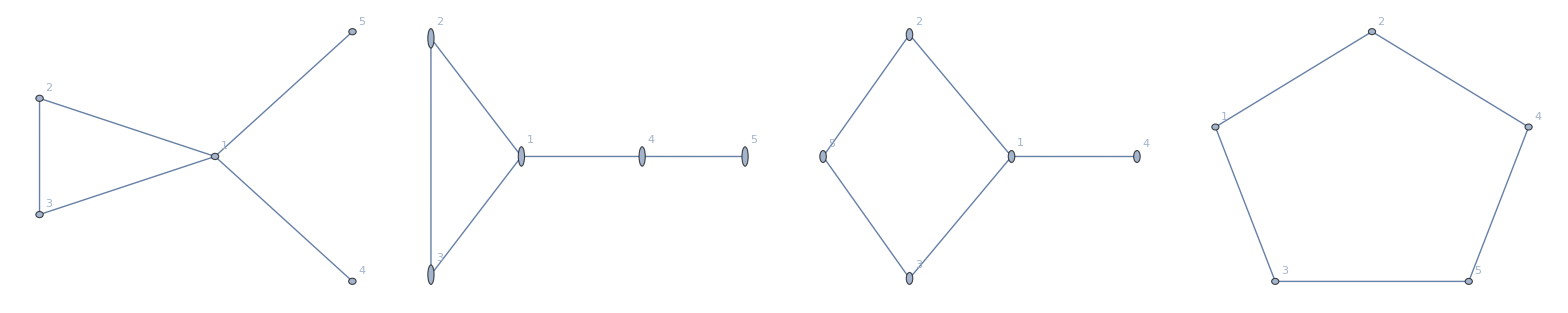

Not Perfect Distance Graphs:

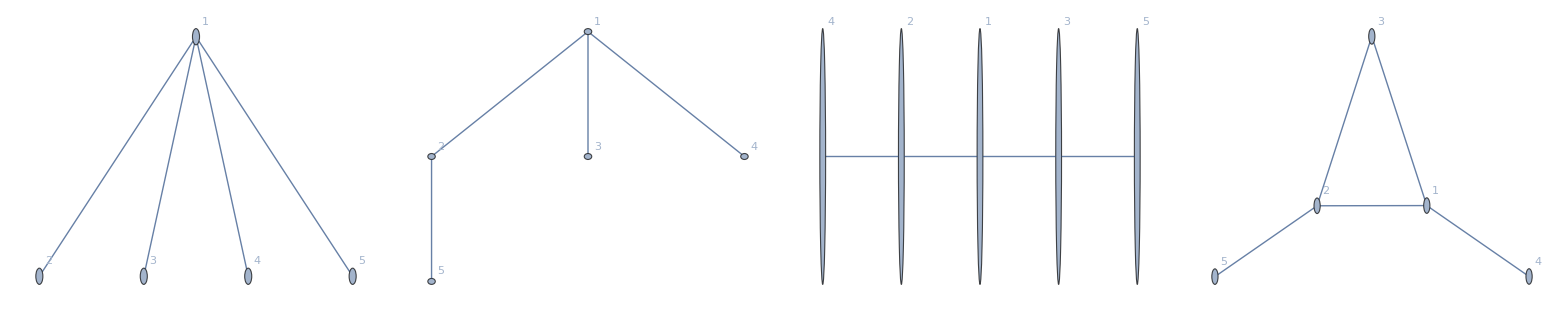

```mathematica
(*CHOOSE SET OF GRAPHS TO TEST*)
GraphList =vertex5;
MinimalPerfectDistanceGraphs = {};
NotPerfectDistanceGraphs = {};

AbsoluteTiming[
While[Length[GraphList]>0,
G = First[GraphList];
GraphList = Delete[GraphList,1];

WL = WeightsList[G];
PDGQ = Catch[Do[If[PerfectDistanceQ[G,w],Throw[True]],{w,WL}]];

If[PDGQ===True,
AppendTo[MinimalPerfectDistanceGraphs,G];GraphList = Select[GraphList,Not[IsomorphicSubgraphQ[G,#]]&];
,AppendTo[NotPerfectDistanceGraphs,G]];

];
]

Print["Minimal Perfect Distance Graphs: "]
TableForm[MinimalPerfectDistanceGraphs,TableDirections->Row]

Print["Not Perfect Distance Graphs: "]
TableForm[NotPerfectDistanceGraphs,TableDirections->Row]
```

```mathematica
GraphList =vertex5;
LStart = Length[GraphList];
lenGL=LStart;
MinimalPerfectDistanceGraphs = {}; NotPerfectDistanceGraphs = {};

P1=ProgressIndicator[Dynamic[(LStart-lenGL)/LStart]]
P2=ProgressIndicator[Dynamic[status/lenW]]

TotalTime = AbsoluteTiming[
While[Length[GraphList]>0,
G = First[GraphList];
GraphList = Delete[GraphList,1];

W = WeightSets[VertexCount[G],EdgeCount[G]];

status=0;
lenW = Length[W];

PDGQ =Catch[Do[
WL = Permutations[Wi];ResWi =Catch[Do[If[PerfectDistanceQ[G,w],Throw[True]],{w,WL}]];If[ResWi===True,Throw[ResWi]];status++,{Wi,W}]];

If[PDGQ===True,
AppendTo[MinimalPerfectDistanceGraphs,G];GraphList = Select[GraphList,Not[IsomorphicSubgraphQ[G,#]]&];
,AppendTo[NotPerfectDistanceGraphs,G];
];
lenGL = Length[GraphList];
];
][[1]];

Print[
"Time To Compute:\t",TimeObject[{0,0,TotalTime}]," and ",1000FractionalPart[TotalTime],"ms\n",
"Minimal Perfect Distance Graphs(",Length[MinimalPerfectDistanceGraphs],"): \n",TableForm[MinimalPerfectDistanceGraphs,TableDirections->Row],"\n",
"Not Perfect Distance Graphs(",Length[NotPerfectDistanceGraphs],"): \n",
TableForm[NotPerfectDistanceGraphs,TableDirections->Row]
]
```